## Test system

```mathematica
Manipulate[
eqs={
s[t_]={s1[t],s2[t],s3[t],s4[t]};
i[t_]={i1[t],i2[t],i3[t],i4[t]};
x[t_]={x1[t],x2[t],x3[t],x4[t]};
z[t_]={z1[t],z2[t],z3[t],z4[t]};

npop=100;
a=0.2;
ϕ=6.69;

τ={52,52,52,52};
ρ={0.2,0.2,0.2,0.2};
μ=1/70.;
α={
{1,0,0,0},
{0,1,0,0},
{0,0,1,0},
{0,0,0,1}
};
β=(*{478.0,495.0,488.0,465.0};*){30,40,50,60};
(*ka=0.0;*)
{{α11,α12,α13,α14},
{α21,α22,α23,α24},
{α31,α32,α33,α34},
{α41,α42,α43,α44}}=α/.{0->ka};

λ[t_]=(1+a Cos[2π(t-ϕ/12)])β i[t];
{λ1[t],λ2[t],λ3[t],λ4[t]}=λ[t];

Λ[t_]=λ[t](1-Total@(x[t]/npop)+x[t]/npop) +{λ1[t]((x1[t]/npop-α11 x1[t]/npop)+(x2[t]/npop-α21 x2[t]/npop)+(x3[t]/npop-α31 x3[t]/npop)+(x4[t]/npop-α41 x4[t]/npop)),λ2[t]((x1[t]/npop-α12 x1[t]/npop)+(x2[t]/npop-α22 x2[t]/npop)+(x3[t]/npop-α32 x3[t]/npop)+(x4[t]/npop-α42 x4[t]/npop)),λ3[t]((x1[t]/npop-α13 x1[t]/npop)+(x2[t]/npop-α23 x2[t]/npop)+(x3[t]/npop-α33 x3[t]/npop)+(x4[t]/npop-α43 x4[t]/npop)),λ4[t]((x1[t]/npop-α14 x1[t]/npop)+(x2[t]/npop-α24 x2[t]/npop)+(x3[t]/npop-α34 x3[t]/npop)+(x4[t]/npop-α44 x4[t]/npop))};

s'[t]==-Λ[t]*s[t]/npop + μ npop-μ s[t],
i'[t]==Λ[t]*s[t]/npop-τ i[t]-μ i[t],
x'[t]==τ i[t]-ρ x[t]-μ x[t],
z'[t]==ρ x[t]-μ z[t],
s[0]=={npop-1,npop-1,npop-1,npop-1},
i[0]=={1,1,1,1},
x[0]=={0,0,0,0},
z[0]=={0,0,0,0}
};
sol=Quiet[NDSolve[eqs,{s[t],i[t],x[t],z[t]},{t,0,60},Method->"StiffnessSwitching"]];
Column[{
Plot[Evaluate[s[t]/.sol][[1,{1,2}]],{t,0,50},PlotRange->{0,Automatic},ImageSize->Medium],
Plot[Evaluate[i[t]/.sol][[1,{1,2}]],{t,0,50},PlotRange->{0,Automatic},ImageSize->Medium],
Plot[Evaluate[x[t]/.sol][[1,{1,2}]],{t,0,50},PlotRange->{0,Automatic},ImageSize->Medium],
Plot[Evaluate[z[t]/.sol][[1,{1,2}]],{t,0,50},PlotRange->{0,Automatic},ImageSize->Medium]
}],
{ka,0,1,0.001,Appearance->"Labeled"},
SynchronousUpdating->False
]
```

## phase plot

```mathematica
Manipulate[
eqs={
s[t_]={s1[t],s2[t],s3[t],s4[t]};
i[t_]={i1[t],i2[t],i3[t],i4[t]};
x[t_]={x1[t],x2[t],x3[t],x4[t]};
z[t_]={z1[t],z2[t],z3[t],z4[t]};

npop=2.0 10^7;
a=0.2;
ϕ=6.69;
τ={52.0,52.0,52.0,52.0};
ρ={rho,rho,rho,rho};
μ=1/70.;
α={
{1,0,0,0},
{0,1,0,0},
{0,0,1,0},
{0,0,0,1}
};
β={478.0,495.0,488.0,465.0};
(*ka=0.0;*)
{{α11,α12,α13,α14},
{α21,α22,α23,α24},
{α31,α32,α33,α34},
{α41,α42,α43,α44}}=α/.{0->ka};

λ[t_]=(1+a Cos[2π(t-ϕ/12)])β i[t];
{λ1[t],λ2[t],λ3[t],λ4[t]}=λ[t];

Λ[t_]=λ[t](1-Total@(x[t]/npop)+x[t]/npop) +{λ1[t]((x1[t]/npop-α11 x1[t]/npop)+(x2[t]/npop-α21 x2[t]/npop)+(x3[t]/npop-α31 x3[t]/npop)+(x4[t]/npop-α41 x4[t]/npop)),λ2[t]((x1[t]/npop-α12 x1[t]/npop)+(x2[t]/npop-α22 x2[t]/npop)+(x3[t]/npop-α32 x3[t]/npop)+(x4[t]/npop-α42 x4[t]/npop)),λ3[t]((x1[t]/npop-α13 x1[t]/npop)+(x2[t]/npop-α23 x2[t]/npop)+(x3[t]/npop-α33 x3[t]/npop)+(x4[t]/npop-α43 x4[t]/npop)),λ4[t]((x1[t]/npop-α14 x1[t]/npop)+(x2[t]/npop-α24 x2[t]/npop)+(x3[t]/npop-α34 x3[t]/npop)+(x4[t]/npop-α44 x4[t]/npop))};

s'[t]==-Λ[t]s[t]/npop + μ npop-μ s[t],
i'[t]==Λ[t]s[t]/npop-τ i[t]-μ i[t],
x'[t]==τ i[t]-ρ x[t]-μ x[t],
z'[t]==ρ x[t]-μ z[t],
s[0]=={npop-1,npop-1,npop-1,npop-1},
i[0]=={1,1,1,1},
x[0]=={0,0,0,0},
z[0]=={0,0,0,0}
};
sol=Quiet[NDSolve[SetPrecision[eqs,Infinity],{s[t],i[t],x[t],z[t]},{t,0,50},PrecisionGoal->ControlActive[4,8],WorkingPrecision->ControlActive[MachinePrecision,20],Method->"StiffnessSwitching"]];
fns=(i[t]/.sol)~Join~(D[i[t]/.sol,t])ᵀ;
(*ParametricPlot[fns[[4]]//Log,{t,0,50}]*)
Plot[fns[[1]],{t,0,50},PlotRange->Full]
,
{rho,0,1,0.001,Appearance->"Labeled"},
{ka,0,1,0.001,Appearance->"Labeled"},
TrackedSymbols->Manipulate
]
```

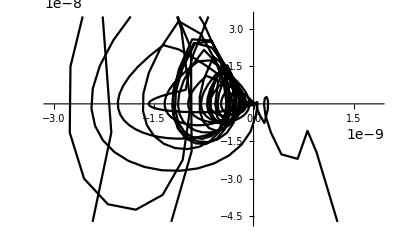
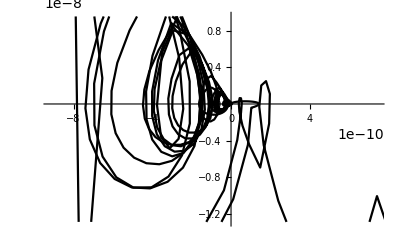
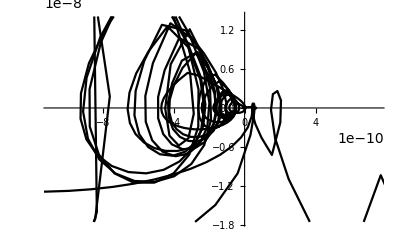
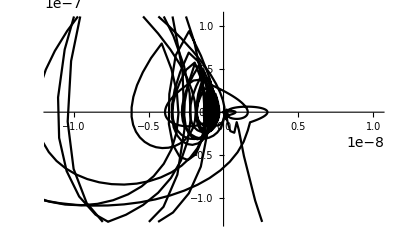

```mathematica
eqs={
s[t_]={s1[t],s2[t],s3[t],s4[t]};
i[t_]={i1[t],i2[t],i3[t],i4[t]};
x[t_]={x1[t],x2[t],x3[t],x4[t]};
z[t_]={z1[t],z2[t],z3[t],z4[t]};

npop=2.0 10^7;
a=0.2;
ϕ=6.69;
τ={52.0,52.0,52.0,52.0};
ρ={rho,rho,rho,rho};
μ=1/70.;
α={
{1,0,0,0},
{0,1,0,0},
{0,0,1,0},
{0,0,0,1}
};
β={478.0,495.0,488.0,465.0};
(*ka=0.0;*)
{{α11,α12,α13,α14},
{α21,α22,α23,α24},
{α31,α32,α33,α34},
{α41,α42,α43,α44}}=α/.{0->ka};

λ[t_]=(1+a Cos[2π(t-ϕ/12)])β i[t];
{λ1[t],λ2[t],λ3[t],λ4[t]}=λ[t];

Λ[t_]=λ[t](1-Total@(x[t]/npop)+x[t]/npop) +{λ1[t]((x1[t]/npop-α11 x1[t]/npop)+(x2[t]/npop-α21 x2[t]/npop)+(x3[t]/npop-α31 x3[t]/npop)+(x4[t]/npop-α41 x4[t]/npop)),λ2[t]((x1[t]/npop-α12 x1[t]/npop)+(x2[t]/npop-α22 x2[t]/npop)+(x3[t]/npop-α32 x3[t]/npop)+(x4[t]/npop-α42 x4[t]/npop)),λ3[t]((x1[t]/npop-α13 x1[t]/npop)+(x2[t]/npop-α23 x2[t]/npop)+(x3[t]/npop-α33 x3[t]/npop)+(x4[t]/npop-α43 x4[t]/npop)),λ4[t]((x1[t]/npop-α14 x1[t]/npop)+(x2[t]/npop-α24 x2[t]/npop)+(x3[t]/npop-α34 x3[t]/npop)+(x4[t]/npop-α44 x4[t]/npop))};

s'[t]==-Λ[t]s[t]/npop + μ npop-μ s[t],
i'[t]==Λ[t]s[t]/npop-τ i[t]-μ i[t],
x'[t]==τ i[t]-ρ x[t]-μ x[t],
z'[t]==ρ x[t]-μ z[t],
s[0]=={npop-1,npop-1,npop-1,npop-1},
i[0]=={1,1,1,1},
x[0]=={0,0,0,0},
z[0]=={0,0,0,0}
}/.{rho->0.9,ka->0};
sol=Quiet[NDSolve[SetPrecision[eqs,Infinity],{s[t],i[t],x[t],z[t]},{t,0,10},PrecisionGoal->ControlActive[4,8],WorkingPrecision->ControlActive[MachinePrecision,20],Method->"StiffnessSwitching"]];
fns=(i[t]/.sol)~Join~(D[i[t]/.sol,t])ᵀ;
ls=Table[Table[fns[[j]]/.t->i,{i,0,10,0.01}],{j,1,4,1}];
Row[Table[ListPlot[ls[[j]],Joined->True,Ticks->None,PlotRange->Automatic,PlotStyle->Black,AxesStyle->Red],{j,4}]]
```

```mathematica
PhasePlot[rho_,ka_,beta_]:=Module[{eqs,fns,ls,sol},
eqs={
s[t_]={s1[t],s2[t],s3[t],s4[t]};
i[t_]={i1[t],i2[t],i3[t],i4[t]};
x[t_]={x1[t],x2[t],x3[t],x4[t]};
z[t_]={z1[t],z2[t],z3[t],z4[t]};

npop=2.0 10^7;
a=0.2;
ϕ=6.69;
τ={52.0,52.0,52.0,52.0};
ρ={rho,rho,rho,rho};
μ=1/70.;
α={
{1,0,0,0},
{0,1,0,0},
{0,0,1,0},
{0,0,0,1}
};
β=beta;
(*{478.0,495.0,488.0,465.0};*)
(*ka=0.0;*)
{{α11,α12,α13,α14},
{α21,α22,α23,α24},
{α31,α32,α33,α34},
{α41,α42,α43,α44}}=α/.{0->ka};

λ[t_]=(1+a Cos[2π(t-ϕ/12)])β i[t];
{λ1[t],λ2[t],λ3[t],λ4[t]}=λ[t];

Λ[t_]=λ[t](1-Total@(x[t]/npop)+x[t]/npop) +{λ1[t]((x1[t]/npop-α11 x1[t]/npop)+(x2[t]/npop-α21 x2[t]/npop)+(x3[t]/npop-α31 x3[t]/npop)+(x4[t]/npop-α41 x4[t]/npop)),λ2[t]((x1[t]/npop-α12 x1[t]/npop)+(x2[t]/npop-α22 x2[t]/npop)+(x3[t]/npop-α32 x3[t]/npop)+(x4[t]/npop-α42 x4[t]/npop)),λ3[t]((x1[t]/npop-α13 x1[t]/npop)+(x2[t]/npop-α23 x2[t]/npop)+(x3[t]/npop-α33 x3[t]/npop)+(x4[t]/npop-α43 x4[t]/npop)),λ4[t]((x1[t]/npop-α14 x1[t]/npop)+(x2[t]/npop-α24 x2[t]/npop)+(x3[t]/npop-α34 x3[t]/npop)+(x4[t]/npop-α44 x4[t]/npop))};

s'[t]==-Λ[t]s[t]/npop + μ npop-μ s[t],
i'[t]==Λ[t]s[t]/npop-τ i[t]-μ i[t],
x'[t]==τ i[t]-ρ x[t]-μ x[t],
z'[t]==ρ x[t]-μ z[t],
s[0]=={npop-1,npop-1,npop-1,npop-1},
i[0]=={1,1,1,1},
x[0]=={0,0,0,0},
z[0]=={0,0,0,0}
};
sol=Quiet[NDSolve[SetPrecision[eqs,Infinity],{s[t],i[t],x[t],z[t]},{t,0,10},PrecisionGoal->ControlActive[4,8],WorkingPrecision->ControlActive[MachinePrecision,20],Method->"StiffnessSwitching"]];
fns=(i[t]/.sol)~Join~(D[i[t]/.sol,t])ᵀ;
ls=Table[Table[fns[[j]]/.t->i,{i,0,10,0.01}],{j,1,4,1}];
Table[ListPlot[ls[[j]],Joined->True,Ticks->None,PlotRange->Automatic,PlotStyle->Black,ImageSize->Small,AxesStyle->Red],{j,4}]
];
```

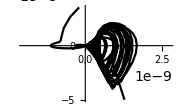
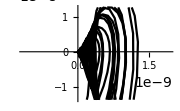
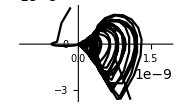
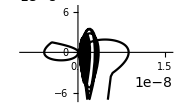

```mathematica
PhasePlot[0.5,0,{478.0,495.0,488.0,465.0}]
```

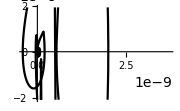
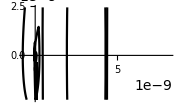
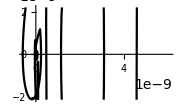
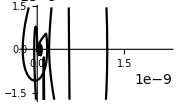
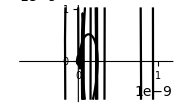
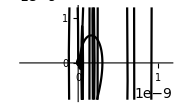
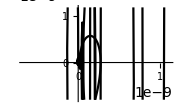
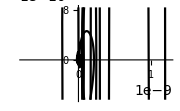
ρ | I_DENV-1 | I_DENV-2 | I_DENV-3 | I_DENV-4
0. | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.1 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.2 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.3 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.4 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.5 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.6 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.7 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.8 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.9 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
1. | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Prepend[Table[{j}~Join~PhasePlot[j,0,{478.0,495.0,488.0,465.0}],{j,0,1,0.1}],{"ρ","I_DENV-1","I_DENV-2","I_DENV-3","I_DENV-4"}],Frame->All]
```

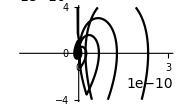
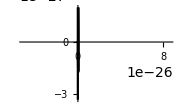
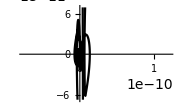
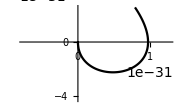
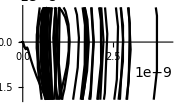
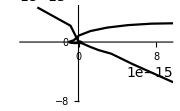
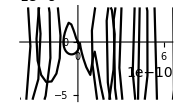
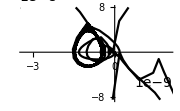
ρ | I_DENV-1 | I_DENV-2 | I_DENV-3 | I_DENV-4
0. | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.1 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.2 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.3 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.4 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.5 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.6 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.7 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.8 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.9 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
1. | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Prepend[Table[{j}~Join~PhasePlot[j,1,{400.0,0.0,0.0,0.0}],{j,0,1,0.1}],{"ρ","I_DENV-1","I_DENV-2","I_DENV-3","I_DENV-4"}],Frame->All]
```

```mathematica
Export["phasetest.png",%]
```

phasetest.png

```mathematica
Directory[]
```

C:\Users\sompob\Documents